```mathematica
f[x_]:=5*(1-Exp[-x])-x
```

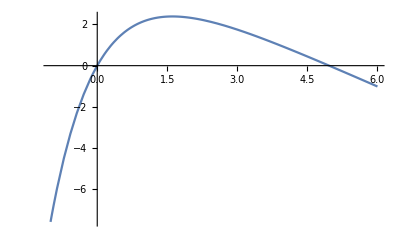

```mathematica
Plot[f[x],{x,-1,6}]
```

```mathematica
(*基于Do执行迭代*)x=2.;
n=3;

Do[x=x-f[x]/f'[x],n]

Print["xRoot ","after ",n," times: ",x]
```

xRoot after 3 times: 4.96513

```mathematica
(*基于While执行迭代*)Clear[x,n]

x=2.;
delx0=0.01;  (*反复调整该参数*)

delx=delx0+1.;
n=0;

While[delx>delx0,x0=x;
x=x-f[x]/f'[x];
delx=Abs[x0-x];
n++]

Print["xRoot ","after ",n," times: ",x]
```

xRoot after 4 times: 4.96511

```mathematica
(*基于Wolfram函数FindRoot执行迭代*)Clear[x]
FindRoot[5*(1-Exp[-x])==x,{x,2.}]
```

{x→4.96511}